```mathematica
F[x_]:=x^2-Cos[x]
PasoNewtonRaphson[x_]:=x-F[x]/F'[x]
FunciónError[x_]:=(-F''[x])/F'[x]
```

```mathematica
NewtonRhapson[xi_,n_]:=Block[{aproximaciones = {xi},x = xi}(*Espero pueda explicar la función Block en clase, porque a pesar de que leí la documentación, no me quedó muy claro. Gracias*),
Do[
x = PasoNewtonRaphson[x];
AppendTo[aproximaciones,x];
,
n-1
];

aproximaciones
];
```

```mathematica
SolucionesPosibles = NewtonRhapson[0.2,10]
```

{0.2,1.77026,1.03321,0.843334,0.824335,0.824132,0.824132,0.824132,0.824132,0.824132}

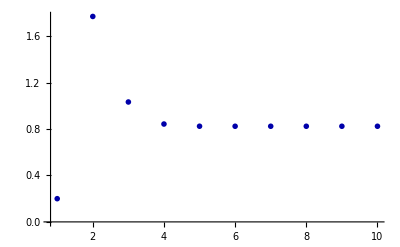

```mathematica
ListPlot[SolucionesPosibles,PlotRange->All, PlotMarkers->{x, Small},PlotStyle->Darker[Blue]]
```

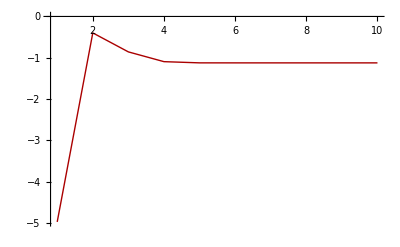

```mathematica
ListLinePlot[Map[FunciónError,SolucionesPosibles],PlotRange->All,PlotStyle->{Thick,Darker[Red]}]
```